```mathematica
Manipulate[
Module[{ΔH,ΔS,R,Keq1,total,eNH3,eN2,eH2,Keq2,z,ζ},
ΔH=-92200;
ΔS=-198.75;
R=8.314;
Keq1=Exp[-(ΔH-T*ΔS)/(R*T)];

(*initialNH3=1;*)
total[x_]=molesNH3+1+molesN2+molesH2-2*x;
eNH3[x_]=molesNH3+1+2*x;
eN2[x_]=molesN2-x;
eH2[x_]=molesH2-3*x;
Keq2=(eNH3[x]/total[x])^2/((eN2[x]/total[x])*(eH2[x]/total[x])^3*P^2);
z=x/.Quiet@Solve[Keq1==Keq2,x,Reals];
ζ=If[eNH3[z[[1]]]<0∨eN2[z[[1]]]<0∨eH2[z[[1]]]<0,z[[2]],z[[1]]
];


Show[
BarChart[{eN2[ζ],eH2[ζ],eNH3[ζ]},ChartStyle->{Green,Blue,Orange},Frame->{{True,False},{True,False}},FrameLabel->{None,Style["number of moles ",17]},
LabelStyle->{Black,13},FrameTicks->{{Automatic,None},{None,None}},ImageSize->500,PlotRange->{0,16},PlotRangeClipping->False,ImagePadding->{{Automatic,None},{Automatic,60}},
ChartLabels->Placed[{
Style[If[eN2[ζ]<0.01,"",Column[{Text@Subscript["N",2],NumberForm[eN2[ζ],{3,2}]},Center]],18],
Style[If[eH2[ζ]<0.01,"",Column[{Text@Subscript["H",2],NumberForm[eH2[ζ],{3,2}]},Center]],18],
Style[If[eNH3[ζ]<0.01,"",Column[{Text@Subscript["NH",3],NumberForm[eNH3[ζ],{3,2}]},Center]],18]},Above]],
Graphics[{
Text[Style[Row[{Subscript["N",2]," + ",Subscript["2H",2]," ⇌ ",Subscript["3NH",3]}],18],{1.25,18}],
Text[Style[Row[{
Subscript[Style["K",Italic],"eq"]," = ",
Superscript[
Row[{"("Subscript[Style["x",Italic],Subscript["NH",3]],")"}],2]/
Row[{
"(",Subscript[Style["x",Italic],Subscript["N",2]],") ",
Superscript[Row[{"(",Subscript[Style["x",Italic],Subscript["H",2]],")"}],3],
Superscript[Style[" P",Italic],2]
}]
}],18],{2.75,18}]
}]
]

],
Grid[{
{Column[{
Null,
Control[{{P,150,"pressure (bar)"},50,250,10,Appearance->"Labeled",ImageSize->Small}],
Control[{{T,500,"temperature (K)"},300,750,10,Appearance->"Labeled",ImageSize->Small}]
}],
Column[{
(*Style["add moles:",Bold],*)
Control[{{molesN2,1,Row[{"add moles ",Subscript["N",2]}]},0,10,0.2,Appearance->"Labeled",ImageSize->Small}],
Control[{{molesH2,1,Row[{"add moles ",Subscript["H",2]}]},0,8,0.2,Appearance->"Labeled",ImageSize->Small}],
Control[{{molesNH3,1,Row[{"add moles ",Subscript["NH",3]}]},0,5,0.1,Appearance->"Labeled",ImageSize->Small}]
}]}
}]
]
```

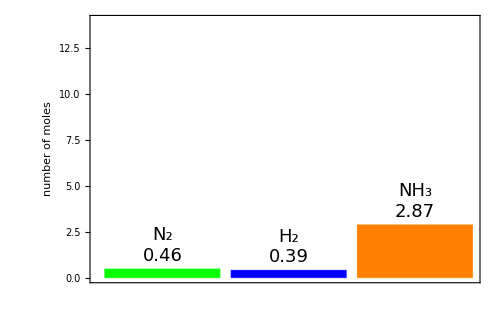
```mathematica
ImageDimensions[-Graphics-]
```

{500,292}

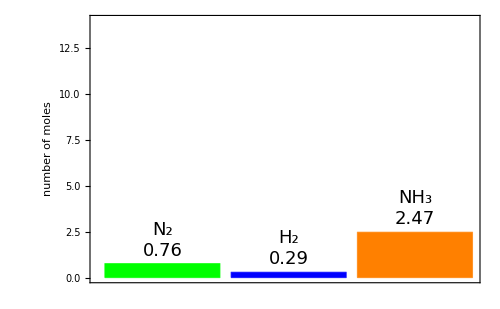
```mathematica
ImageDimensions[-Graphics-]
```

{500,499}